# Pitch Perception: Missing fundamentals and Shepard tones

Ctrl-A followed by Shift-Enter to Evaluate all cells to ensure proper sound
Please Ignore code snippets and read text highlighted in blue and figures only.

## Init code

```mathematica
Clear[playbutton]
playbutton[freqamp_List]:=Module[{freq=First/@freqamp,amp=Last/@freqamp,f},
f[t_]=Sum[amp⟦i⟧ Sin[2 Pi freq⟦i⟧ t],{i,1,Length[freqamp]}];
Button[Column[First/@freqamp "Hz"],EmitSound@Play[f[t],{t,0,.25},SampleRate->8000]]
];
```

```mathematica
timeseries[freqamp_List]:=Module[{freq=First/@freqamp,amp=Last/@freqamp,f},
f[t_]=Sum[amp⟦i⟧ Sin[2 Pi freq⟦i⟧ t],{i,1,Length[freqamp]}];
Table[f[t],{t,0,.25,1/8000.}]
]
```

```mathematica
Module[{play,semitone}, (* defines array scale *)
play[freqamp_List]:=Module[{f,freq=First/@freqamp,amp=Last/@freqamp},
f[t_]=Sum[amp⟦i⟧ Sin[2 Pi freq⟦i⟧ t],{i,1,Length[freqamp]}];
Play[f[t],{t,0,.25}]
];
semitone=2^Table[i/12,{i,0,12}];

Clear[double];
double[{f1_,0},a2_]:=Module[{f,a,nmax,zmin=-3,zmax=3},
f=Table[s f1,{s,semitone}];
nmax=Length[f];
a=Range[0,a2,(a2-0)/(nmax-1)];
Part[a,1]=0;
Part[a,-1]=a2;
Thread[{f,a}]
];
double[{f1_,a1_},a2_]:=Module[{f,a,nmax},
f=Table[s f1,{s,semitone}];
nmax=Length[f];
a=Range[a1,a2,(a2-a1)/(nmax-1)];
Thread[{f,a}]
];

Module[{wa},
wa={double[{250,0.5},1.75],
double[{500,1.75},1.0],
double[{750,2.5},0.25],
double[{1000,1},0.05],
double[{1250,0.5},0],
double[{1500,0.25},0],
double[{1750,0.15},0],
double[{2000,0.05},0],

double[{375,0},2.5],
double[{625,0},0.5],
double[{875,0},0.15]
};
PrependTo[wa,Thread[{250,.5LogisticSigmoid/@Range[-6.,6.,1.]}]];
scale=Table[play[Flatten[wa⟦All,n⟧,{1}]],{n,1,13}]
]];
```

## Missing fundamental

Click Rectangular Buttons in notebook to hear sound

```mathematica
Panel[{playbutton[{{400,1}}],"\t",playbutton[{{400,1},{600,.25}}]},Style["Example 1",Background->Lighter[Cyan,.8]]]
```

{400 Hz,	,400 Hz
600 Hz}Example 1

Each button represents a sound which is a mixture of pure sine waves with the given frequencies.
Introducing a higher frequency of 600 Hz surprisingly makes the perceived pitch sound lower.

```mathematica
Panel[{playbutton[{{300,1},{600,1}}],"\t",playbutton[{{400,1},{600,.4}}]},Style["example 2",Background->Lighter[Cyan,.9]]]
```

{300 Hz
600 Hz,	,400 Hz
600 Hz}example 2

Replacing 300 Hz by the higher 400 Hz  again, surprisingly makes the perceived pitch sound lower

```mathematica
Panel[{Labeled[playbutton[{{250,1.},{500,0.25},{1000,.08}}],
Style["A",18]],
Labeled[playbutton[{{250,1.},{375,1.75},{500,1.5},{1000,.25}}],Style["B",18]]},Style["example 3",Background->Lighter[Cyan,.9]]]
```

{250 Hz
500 Hz
1000 HzA,250 Hz
375 Hz
500 Hz
1000 HzB}example 3

A:   The first 3 overtones of  a 250 Hz pitched sound.
Therefore A is perceived to have a pitch of 250 Hz.

B: By introducing 350 Hz which is higher than 250 Hz we might expect B to sound higher in pitch than A. Again, surprisingly  B is perceived to have a pitch one octave lower that A.

As reference, we provide the sound of pure sine waves:

```mathematica
DynamicModule[{fa},
fa={{250,1},{375,2},{500,2.5},{1000,.5}};
Map[playbutton[{#}]&,fa]
]
```

### Frequency domain discussion

Any  periodic waveform consists of frequencies which are integer multiples 
                                                                                          1 f_0  2 f_0   3 f_0   4 f_0.....
of a fundamental frequency f_0. A naturally produced  sound from a linear instrument will have a dominant contribution at the fundamental f_0 and smaller contributions in the overtones 2 f_0   3 f_0   4 f_0......  However synthetic waveforms where the f_0 contribution is missing  may be created. This is quite obvious in Examples 1 and 2 where the second tone has a missing fundamental of 200Hz. Example 3 has the structure of:
                                                                                      1 f_0  2 f_0   3 f_0                                   with f0 = 250   for   (A)
                                                                                                        __    2 f_0   3 f_0   4 f_0  ...8 f_0             with f0 = 125   for   (B)
which shows that B has the missing fundamental of 125 Hz. (It is also missing harmonics 5,6,7)
A standard explanation for why such synthetic periodic waveforms with a missing fundamental like B are still perceived to have a pitch of f_0 is that the ear somehow fills in for this missing fundamental.

### Time domain discussion

But it is the time domain that reveals exactly why B is perceived to have a pitch one octave lower than A, in example 3 and similarly in example1 and 2

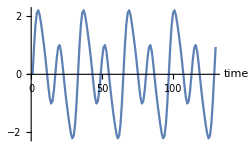
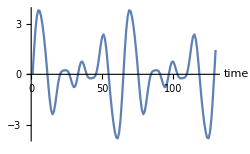
{-Graphics-A,-Graphics-B}

```mathematica
Module[{ts1,ts2,is=ImageSize->250},
ts1=timeseries[{{250,1.},{500,1.5},{1000,.25}}];
ts2=timeseries[{{250,1.},{375,1.75},{500,1.5},{1000,.25}}];
{Labeled[ListLinePlot[Take[ts1,130],is,AxesLabel->{Style["time",15],""}],Style["A",18]],
Labeled[ListLinePlot[Take[ts2,130],is,AxesLabel->{Style["time",15],""}],Style["B",18]]}
]
```

Let us look the waveforms for sounds A and B of example 3 in Figure above. We observe that:
Waveform  A  repeats every 32 samples or 250 times a second  -  its perceived pitch.
Waveform  B repeats every 64 samples or 125 times a second  -  its perceived pitch.
Suddenly, everything is clear. Introducing the faster 350Hz component into A  makes the new waveform B repeat at a slower rather than faster rate! Why is this? Let us look more closely.  As we saw the addition of 375 Hz transforms the harmonic series
                                                                                      1 f_0  2 f_0   3 f_0                           with f0 = 250   for   (A)
into                                                                                                        2 f_0   3 f_0   4 f_0.....           with f0 = 125   for  (B)
Thus B is just another harmonic series except with a missing fundamental. Removing a fundamental frequency from a waveform cannot change its periodic nature nor indeed the frequency at which it repeats which is still  f_0 cycles a second.

The metaphor  in the figure below may help drive the point home. A red light flashed every 3 seconds. We combine this with a yellow light that flashes  faster - every 2 seconds. But the combined pattern “flashes” (i.e. repeats) slowerI  once every 6 seconds.

Measuring the peak to peak distance in autocorrelation functions of the waveforms is a more principled way of seeing this.

Autocorrelation functions

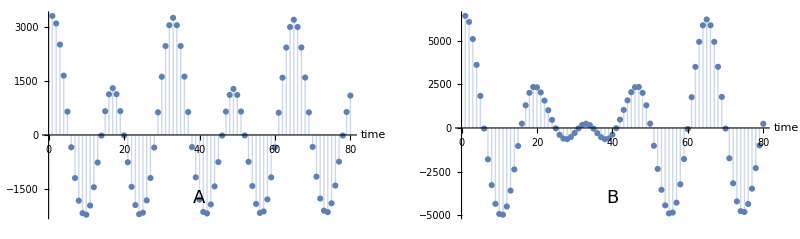

```mathematica
Module[{ts1,ts2,ac1,ac2},
ts1=timeseries[{{250,1.},{500,1.5},{1000,.25}}];
ts2=timeseries[{{250,1.},{375,1.75},{500,1.5},{1000,.25}}];
ac1=ListCorrelate[ts1,ts1,{1,-80},0];
ac2=ListCorrelate[ts2,ts2,{1,-80},0];
Print["\t\t\t\t",Style["Autocorrelation functions",18]];
GraphicsRow[{
ListPlot[ac1,Filling->Axis,AxesLabel->{"time",""},Epilog->Text[Style["A",18],Scaled[{.5,.1}]]],
ListPlot[ac2,Filling->Axis,AxesLabel->{"time",""},Epilog->Text[Style["B",18],Scaled[{.5,.1}]]]}]
]
```

Figure above shows the autocorrelation functions for waveforms A and B of example 3
The peak to peak distance in the autocorrelation functions confirms that the waveforms repeat every 32 and 64 samples respectively i.e. with frequencies of 250 and 125 Hz resp as was already evident by direct inspection of the waveforms.

Satisfying though our time domain explanation is, one nevertheless  is left with the nagging feeling: that surely pitch should have something to do with frequency spectrum? For example, of two spectra, should not the one whose frequency spectrum’s center-of-mass is larger also sound higher pitched?  In spite of us showing that this is not the case in all that has preceded we now demonstrate there is indeed some merit to this intuition also! Let us return to example 2. Instead of making a sudden change from 300 Hz  to 400 Hz let us creep gradually up onto 400 Hz.

```mathematica
{Labeled[playbutton[{{ 300,1},{600,.4}}],1],
                Labeled[playbutton[{{ 330,1},{600,.4}}],2],
                Labeled[playbutton[{{ 360,1},{600,.4}}],3],
                Labeled[playbutton[{{ 400,1},{600,.4}}],4]
}
```

{300 Hz
600 Hz1,330 Hz
600 Hz2,360 Hz
600 Hz3,400 Hz
600 Hz4}

From left to right each successive note sounds decidedly higher in pitch. Listen to the sequence 1-2-3-4 and then 1 again. To the author at least, now 1 sounds lower than 4, in contradiction to what was perceived in example 2 above. The reader is invited to return to example 2 and convince herself that the corresponding notes there are exactly the same. It appears that there is a sort of hysteresis, a kind of memory as it were, in pitch perception,  where we are influenced by the history of what we have recently heard. While this conclusion of ambivalence may be disappointing, it presents one with the possibility of exploiting it In order to lead to some striking aural illusions. Here is the idea.

## Cyclic tones (Shepherd tones)

Imagine continuously transforming  the set of frequencies 
										1 f_0  2 f_0   3 f_0   4 f_0..... 
 into the set of frequencies 
                                                                                                                    2 f_0   3 f_0   4 f_0..... 
 as indicated schematically by the arrows in the Figure below.

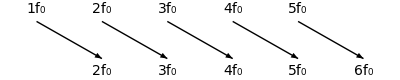

```mathematica
Module[{a,b,fs=14,arr},
a=Table[Text[Style[ToString[n]<>"f_0",fs],{n,1}],{n,1,5}];
b=Table[Text[Style[ToString[n]<>"f_0",fs],{n,0}],{n,2,6}];
arr=Table[Arrow[{{n,1-.2},{n+1,0+.2}}],{n,1,5}];
Graphics[{a,b,arr}]]
```

Each small step in the direction of the arrows must surely increase the perceived pitch. Yet our final configuration of frequencies is identical to the starting one except that f_0  is missing.  But this is just the missing fundamental! So we might expect  the final pitch to be the same as the starting pitch! Incredibly enough, this illusion is real. There are many ways of implementing it but the above remains the central idea. 

Instead of a purely continuous transformation we choose to divide up our transformation into 12 equal logarithmic steps so as to give a sense of moving in musical semi tones. The listener is invited to decide which of these 12 notes is the starting one and which the ending in the sense indicated in the above figure (click on dot). It is difficult to tell. The illusion, of course, is that each successive note clockwise is always increasing!

Click Dots to hear sound

```mathematica
DynamicModule[{θ1=Pi,θ2=3 Pi,dθ=2 Pi/12,θposn,pt,keys},
θposn=Table[θ1+n dθ,{n,0,12}];
pt=Table[{Cos[θ],Sin[θ]},{θ,θposn}];
keys=Table[With[{p=pt⟦i⟧,s=scale⟦i⟧},
                    EventHandler[Point[p],{"MouseClicked":>EmitSound[s]}]],{i,1,12}];
Dynamic[Graphics[{Circle[{0,0},1],PointSize[.08],keys}],SaveDefinitions->True]
]
```

Our approach is somewhat differently motivated from the standard approach ascribed to Mr. Shepard that does not rely on the missing fundamental per se. We implemented this other point of view^(1)) also (below) for comparison. This method  simply relies on a fade-in of the rising lower frequencies and a fade-out of the rising upper ones. Each tone consist of 3 frequencies an octave apart as shown in the spectrogram. The changing line-spectrum in the animation below clearly reveals how these three frequencies are gradually faded in and faded out to help achieve the magic trick.

```mathematica
Hyperlink["1) wiki","https://en.wikipedia.org/wiki/Shepard_tone"]
```

[1) wiki](https://en.wikipedia.org/wiki/Shepard_tone)

An Infinite Keyboard

Click on any key to hear sound.
“do” “re” “...labels guide you to play a major scale
Top Left Tab selector allows you to select any desired key as the tonic “do”